Alejandro Salazar Lobos 		ID: 1517982
Phys362 		Assignment #4

(i) Plot f(t) = h · exp(-t^2/(2 σ^2)) and name it:

Define variable T ≡ t/(√2 σ), and function F(T) ≡ (f(t))/h;
code:

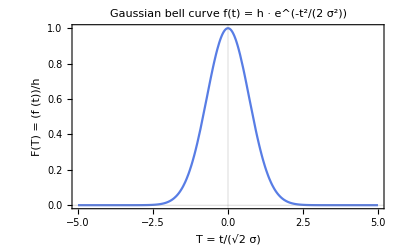

```mathematica
(* Define function *)
F = Exp[-T^2];

(* Plot function *)
Plot[F,{T,-5,5}, FrameLabel -> {"T = t/(√2 σ)", "F(T) = (f (t))/h"}, PlotTheme -> {"Scientific","BoldColor"},PlotLabel -> "Gaussian bell curve f(t) = h · e^(-t^2/(2 σ^2))"]
```

This is the Gaussian bell curve.

(ii) Take the Fourier transform:

g(ω) = 1/(2π)∫_(-∞)^∞ f(t)e^iωt ⅆt

g(ω) = 1/(2π)∫_(-∞)^∞ h·e^(-t^2/(2 σ^2))e^iωt ⅆt

Substitution: T ≡ t/(√2 σ) ⇒ dT/dt=1/(√2 σ)⇒ dt = √2 σ dT:

⇒ g(ω) = 1/(2π)(√2 σ)∫_(-∞)^∞ h·e^(-T^2)· e^(i ω  √2 σ T)ⅆT

Define W = √2 σ ω:

g(ω) = (√2 σ·h)1/(2 π)∫_(-∞)^∞ e^(-T^2)· e^iWTⅆT

Let G(W) ≡ (g(ω))/(√2 σ h)=1/(2π)∫_(-∞)^∞ e^(-T^2)·e^iWTⅆT


So G(W) is the Fourier transform of F(T) = e^(-T^2).

The following code calculates G(W):

```mathematica
(* Calculate the Fourier transformation G(W) of the function F(T) *)
```

```mathematica
G = Integrate[(1/(2*Pi))*(Exp[-T^2])*(Exp[I*W*T]),{T,-Infinity,Infinity}]
```

(ⅇ^(-W^2/4))/(2 √π)

G(W) = 1/(2 √π)·exp(-W^2/4)

The Fourier transform of the original function,  f(t) = h · exp(-t^2/(2 σ^2)) , is therefore:

g(ω) = G(W) · √2 σ h  

= (σ h)/(√(2π)) exp(-W^2/4)

Recall: W = √2σ ω :

g(ω) = (σ h)/(√(2π))exp((-2 σ^2 ω^2)/4)

g(ω)=(σ h)/(√(2π))e^(-(σ^2 ω^2)/2)

∴ The Fourier transform of the function  f(t) = h · exp(-t^2/(2 σ^2))  is g(ω)=(σ h)/(√(2π))e^(-(σ^2 ω^2)/2). // Answer

(iii) Plot the frequency spectrum of the Fourier transform g(ω):

Code:

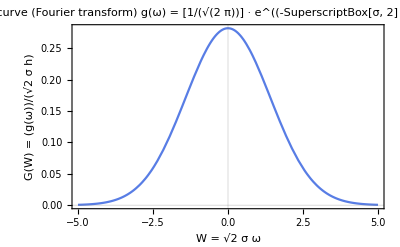

```mathematica
(* Plot the frequency spectrum *)
Plot[G,{W,-5,5}, FrameLabel -> {"W = √2 σ ω", "G(W) = (g(ω))/(√2 σ h)"}, PlotTheme -> {"Scientific","BoldColor"},PlotLabel -> "Gaussian bell curve (Fourier transform) g(ω) = [1/(√(2  π))] · e^((-SuperscriptBox[σ, 2] SuperscriptBox[ω, 2])/2)"]
```

The Fourier transform of a Gaussian bell curve is another Gaussian. The width and height of the transform g(ω) will depend on the value of σ. For example, in the original function f(t), the width of the curve is σ (Pedrotti, p. 241); comparing the form of the exponential of g(ω) with that of f(t), we can conclude that the width of the transform g is 1/σ. Whether the transform g is wider or thinner than the original function f  will depend on the value of σ. In particular, if 0 < σ^2 < 1, we get a wider curve; for σ^2>1, a thinner curve, and for σ^2=1, the same width. Regarding the height, it will also depend on the value of σ and on how larger or smaller it is compared to √(2π): σ < √(2π), the curve is shorter; σ >√(2π), the curve is taller (and thinner), and σ = √(2π), the same height (and thinner). Notice, however, that σ cannot meet the two equality cases at the same time, so we cannot get the same width and height for both curves at the same time.